```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/johannesk/kette_repo/limit_cycles/src_mathematica/good_fits

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
a0a1NUCLmartinrimas=Import["../a0-a1_nucl_Rimas-Martin.dat","Table"][[2;;]];
(* λ C0,D0 (Martin, 23) C0,D0 (Rimas, unprojected, 45) C0,Do (Rimas, projected, 67)*)
LECsNUCLmartinrimas=Import["../LECs_nucl_Rimas-Martin.dat","Table"][[2;;]];
LECsUNITmartinrimas=Import["../LECs_univ_Rimas-Martin.dat","Table"][[2;;]];

(*activeLEC=LECsNUCLmartinrimas[[All,{1,2,3}]];*)
activeLEC=LECsUNITmartinrimas[[All,{1,2,3}]];
```

```mathematica
hbar=197.327053;
Mm=938.92;
m1=3 Mm;m2=3 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]

dimerCores={{2.00,{{3.49894,20.5763},{1.31002,2.03082},{0.230922,56.5742},{0.136023,20.549},{0.146917,20.5961}}}};
λRange=Range[1,Length[activeLEC]];
```

ℏ^2/(2  μ) = 13.8237

```mathematica
RiccatiBesselJ[z_,l_]:=z SphericalBesselJ[l,z];
RiccatiBesselN[z_,l_]:=(-1)^l z SphericalBesselY[l,z];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha[ra_,ka_,la_,ha_]:=RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]

beta[rb_,kb_,lb_,hb_]:=RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])
```

```mathematica
NormTF[core_?ArrayQ]:=1/Sqrt[Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]]core[[k]][[1]]core[[l]][[1]] (Pi^6/27)(1/((core[[i]][[2]]+core[[j]][[2]])(core[[k]][[2]]+core[[l]][[2]])))^6,{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];

VlocTF[r_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_]:=Block[{eta1,eta2,eta3,w1,w2,w3},
eta2= 3^(7/2)Cc /(((Aa+Bb)(Gg+Hh)(2 lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2 lam+3Gg+3Hh)))^(3/2));
w2= 3(Aa+Bb)(Gg+Hh)lam/(2lam Bb+Gg(2 lam+3Bb)+2 lam Hh+3Bb Hh+Aa(2lam+3Gg+3Hh));
eta3 =3^(7/2)Dd /(((Aa+Bb)(lam+Gg+Hh)(lam Bb+Gg(4lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh)))^(3/2));
w3 = 6(Aa+Bb)(Gg+Hh)lam/(lam Bb+Gg(4 lam+3Bb)+4 lam Hh+3Bb Hh+Aa(lam+3Gg+3Hh));
eta1 =3^(7/2)Dd /(((Gg+Hh)(4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))))^(3/2));
w1=(3(Aa+Bb)lam(Aa+Bb+2lam)(Gg+Hh))/((4 lam^2 Bb+2lam Bb^2+Gg(lam^2+8 lam Bb+3Bb^2)+lam^2 Hh+8 lam Bb Hh+3Bb^2 Hh+Aa^2(2lam+3Gg+3Hh)+Aa(Gg(8 lam+6Bb)+4lam(lam+2Hh)+Bb(4lam+6Hh))));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]+eta1 Exp[-w1 r^2]
];

WnolocTF[r_,rp_,Ee_,lam_,Cc_,Dd_,Aa_,Bb_,Gg_,Hh_,Ll_,TwoMyOverHBsq_]:=Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3},
zeta1=0;
a1=4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh;
b1=2Gg Bb -Gg Hh -2 Aa Bb +2 Aa Hh;
c1=Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh;

zeta2=0;
zeta3=0;

a2=4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh);
b2=Gg(4lam+2Bb-2 Hh)+Aa(-4lam-2Bb+2Gg);
c2=Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh);

a3= 4Bb(2lam+Hh)+Gg(Aa+2lam+Hh)+Aa(2lam+Bb+Hh);
b3=Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb);
c3=Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh);

-(4 Pi r rp) (
zeta1 Exp[-a1 r^2-c1 rp^2] ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)+(Ll+1) Ll/r^2-TwoMyOverHBsq Ee) I^Ll  SphericalBesselJ[Ll,I b1 r rp]
-4 a1 b1 r rp Sum[(1-Ll^2+l^2) I^(l+1)/Sqrt[3] (2/Sqrt[5])^((Ll+l)/2) SphericalBesselJ[1+l,I b1 r rp],{l,-Ll,Ll}])
+I^Ll zeta2 SphericalBesselJ[Ll,I b2 r rp] Exp[-a2 r^2-c2 rp^2]
+I^Ll zeta3 SphericalBesselJ[Ll,I b3 r rp] Exp[-a3 r^2-c3 rp^2]
)
];
```

```mathematica
SolveSecular[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},

hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=NormTF[a00];

Wmat=ConstantArray[0,{Npoints,Npoints}];

prefac=(*(4 π)^1.5*)1;

Wmatt=ParallelTable[
cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;
DiagonalMatrix[Table[-cij hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]]
,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmatt,4];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];
(*Print[(Chop[Wmat])[[1;;4,1;;4]]//MatrixForm];*)
Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];

tanDelta= (RiccatiBesselJ[momentum  Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);
(*Print["N_terms = ",Length[a00]^4," calculated for E_rel = ",energyMeV," MeV"];*)
tanDelta
];
```

```mathematica
GetERE[l_,rMax_,nPoints_,core_]:=Module[{locall=l},

dataS={};
tanDsL={};
tanDs={};

eRange=Range[0.01,0.1,0.03];

LECc = Flatten[Select[activeLEC,#[[1]]==locall&]][[2]];
LECd = Flatten[Select[activeLEC,#[[1]]==locall&]][[3]];

SetSharedVariable[tanDs];

Do[
momFM=Sqrt[mh2 energ];
TanDelSwave=SolveSecular[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
AppendTo[tanDs,{energ,TanDelSwave}];
,{energ,eRange}];

tanDs=Reverse[Sort[tanDs,#1[[1]]>#2[[1]]&]]; (*Sort all the momentum since it is parallel*)

(*Extract the ERE Parameters*)
Lrel = 0;
dataS=Transpose[{Sqrt[mh2 eRange],Sqrt[mh2 eRange ]/Re[tanDs⟦All,2⟧]}];
EreS=Fit[dataS⟦1;;3⟧,{1,p^2},p];
a0tf=-Coefficient[EreS,p,0]^-1;
r0tf= Coefficient[EreS,p,2]*2.;
{a0tf,r0tf,dataS}
]
```

```mathematica
(*JacobiTrailWavefunctionPara={{3.765815,7.217888,5.497260},{-1.031541222,7.217888,0.122223},{-0.81558642365,1.497478,0.122223},{-0.26860177627,0.124999,0.122223},{0.38054820786,11.420429,0.077848},{1.5081514531,4.030632,0.077848},{1.7809899176,0.741144,0.249935}};*)
JacobiTrailWavefunctionPara={{-0.6309729502,3.610344,8.616309},{1.31959784,3.610344,0.590896},{0.00072330654655,3.610344,0.214470},{0.19047309014,3.610344,0.058246},{0.74733463307,3.386390,8.616309},{-2.3064434687,3.386390,0.590896},{-0.025916480015,3.386390,0.214470},{-0.3168552366,3.386390,0.058246},{-0.0067247217067,2.925745,8.616309},{1.0528775917,2.925745,0.590896},{0.13905708063,2.925745,0.214470},{0.15802126721,2.925745,0.058246},{-0.073957423699,1.027248,8.616309},{0.00088136264965,1.027248,0.590896},{0.19192964024,1.027248,0.214470},{0.043865816403,1.027248,0.058246},{0.031711236933,0.276734,8.616309},{0.0092070484095,0.276734,0.590896},{0.067895565104,0.276734,0.214470},{0.06625132575,0.276734,0.058246},{-0.038350525283,0.180330,8.616309},{0.030031853144,0.180330,0.590896},{-0.10071785084,0.180330,0.214470},{-0.13503726328,0.180330,0.058246},{0.018779041355,0.147670,8.616309},{-0.019756959754,0.147670,0.590896},{0.087438072826,0.147670,0.214470},{0.11365643511,0.147670,0.058246},{-0.000025540721652,0.011305,8.616309},{0.00007185049035,0.011305,0.590896},{-0.00017076191518,0.011305,0.214470},{0.000060827663351,0.011305,0.058246},{0.018058858687,9.799701,3.934908},{0.0015754735742,9.799701,0.476404},{0.001151199067,9.799701,0.120846},{-0.00035810276122,9.799701,0.004681},{0.10518234804,3.839041,3.934908},{-0.027961936557,3.839041,0.476404},{-0.011575549426,3.839041,0.120846},{-0.0008064455784,3.839041,0.004681},{0.32469249853,1.896162,3.934908},{-0.15519664327,1.896162,0.476404},{-0.018656774725,1.896162,0.120846},{-0.018621206351,1.896162,0.004681},{0.19472993703,0.996058,3.934908},{-0.1144428087,0.996058,0.476404},{-0.037477555697,0.996058,0.120846},{-0.00598292178,0.996058,0.004681},{-0.038008423969,0.450548,3.934908},{-0.021946557624,0.450548,0.476404},{-0.027700841654,0.450548,0.120846},{-0.011121864493,0.450548,0.004681},{-0.0012489970478,0.097635,3.934908},{-0.038615859221,0.097635,0.476404},{-0.0025366067167,0.097635,0.120846},{-0.024333431955,0.097635,0.004681},{0.0028639932187,0.074197,3.934908},{0.021892983204,0.074197,0.476404},{0.013659028161,0.074197,0.120846},{0.024267549691,0.074197,0.004681},{-0.0012744144182,0.054524,3.934908},{-0.0028802135294,0.054524,0.476404},{0.0030834300287,0.054524,0.120846},{-0.010781194305,0.054524,0.004681}};
Rmax=3;
grdPoints=50;
r1r2Range=Subdivide[Rmax,grdPoints-1];
JacobiTrailWavefunction=Total[#[[1]] Exp[-#[[2]] r1^2]Exp[-#[[3]] r2^2]&/@JacobiTrailWavefunctionPara];
JacobiTrailWavefunctionData=Table[JacobiTrailWavefunction/.{r1->R1,r2->R2},{R1,r1r2Range},{R2,r1r2Range}];
JacobiTrailWavefunctionDataF=Flatten[Table[{R1,R2,JacobiTrailWavefunction/.{r1->R1,r2->R2}},{R1,r1r2Range},{R2,r1r2Range}],1];
```

```mathematica
FitCoreToGauss[nGauss_,core_,ami_:-10,ama_:10,bmi_:0.0,bma_:10]:=Module[{nk,amin,amax,bmin,bmax},
nk=nGauss;
amin=ami;amax=ama;
bmin=bmi;bmax=bma;
modelCluster={Sum[aLn@i Exp[-bLn@i (1./4. rrel1^2+1./3. rrel2^2)],{i,nk}],Table[{amin<aLn@i <amax,bmin<bLn@i <bmax},{i,nk}]};
nlmLABC=NonlinearModelFit[core,modelCluster,Flatten[Table[{{aLn@i,RandomReal[{0.1 amin,0.2 amax}]},{bLn@i,RandomReal[{bmin,bmax}]}},{i,nk}],1],{rrel1,rrel2},Weights->((#1^2+#2^2)^0.5&)];
nlresi=nlmLABC["FitResiduals"];
basispara=Table[{aLn@i,bLn@i},{i,nk}]/.nlmLABC["BestFitParameters"];
basispara
]
```

1) a_(trimer - trimer) = -0.0186933

2) a_(trimer - trimer) = -0.018693

$Aborted

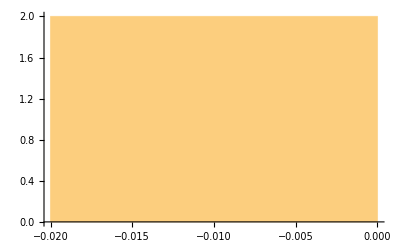

```mathematica
results={};
fitDim=4;
rMax=20;
nGrd=100;
nIter=50;
Do[
tmpCore=FitCoreToGauss[fitDim,JacobiTrailWavefunctionDataF,RandomReal[{-100,0}],RandomReal[{100,1000}],0,RandomReal[{30,60}]];

tmp=GetERE[2,rMax,nGrd,tmpCore];

AppendTo[results,tmp[[1]]];
Print[nn,") a_(trimer - trimer) = ",results[[-1]]]
,{nn,Range[nIter]}]
Histogram[results,{0.02}]
```